```mathematica
Norm[1+Exp[-0.5*I]]^2/2
```

1.87758

```mathematica
1+Cos[1]
```

1+Cos[1]

```mathematica
N[1+Cos[0.5]]
```

1.87758

```mathematica
data=Import["C:\\Users\\Nora\\Documents\\G1.5\\StrucFac\\plot.xlsx",{"Data",2}];
```

```mathematica
Dimensions[data]
```

{801,22}

## 2D square lattice

```mathematica
lattice2D = data[[All,1;;6]];
```

```mathematica
square100 = lattice2D[[All,{1,2}]];
```

```mathematica
square400 = lattice2D[[All,{1,3}]];
```

```mathematica
square625 = lattice2D[[All,{1,4}]];
```

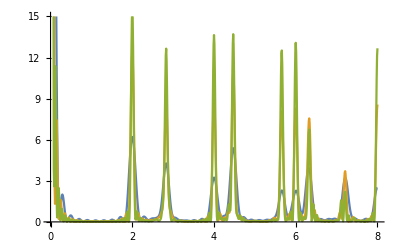

```mathematica
ListLinePlot[{square100,square400,square625},PlotRange->{0,15}]
```

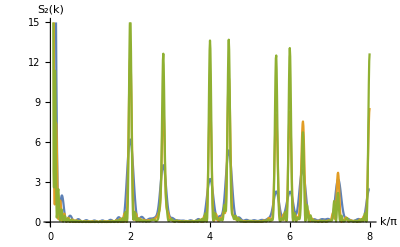

```mathematica
Show[%271,AxesLabel->{HoldForm[k/π],HoldForm["\!\(\*SubscriptBox[\(S\), \(2\)]\)(k)"]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

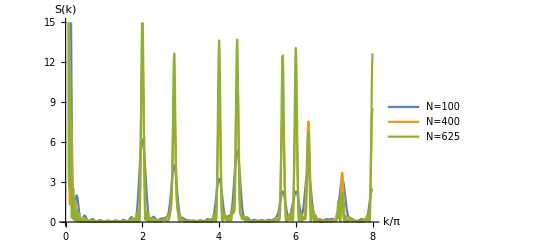

```mathematica
ListLinePlot[{square100,square400,square625},PlotRange->{0,15},PlotLegends->{"N=100","N=400","N=625"},AxesLabel->{HoldForm[k/π],HoldForm["S(k)"]},PlotLabel->None,LabelStyle->{GrayLevel[0]},PlotStyle->Scientific]
```

```mathematica
sqcsv = Import["C:\\Users\\Nora\\Documents\\G1.5\\StrucFac\\squareLattice2D900.csv",{"Data"}]
```

{{0.,0.,900.},{0.,0.05,81.2238},{0.,0.1,40.8635},14635,{6.,5.9,40.8635},{6.,5.95,81.2238},{6.,6.,900.}}
 |  |  |  |

```mathematica
ListPlot3D[sqcsv,PlotRange->{0,100}]
```

-Graphics3D-

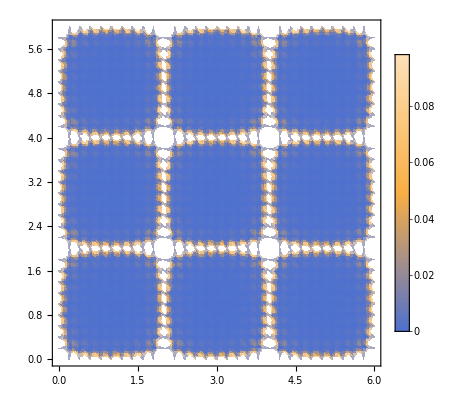

```mathematica
ListDensityPlot[sqcsv,PlotTheme->"Business"]
```

## 2D triangle lattice

```mathematica
triangle2D = data[[All,14;;22]];
```

```mathematica
triang100=triangle2D[[All,{1,2}]];
triang400 = triangle2D[[All,{1,3}]];
triang900 = triangle2D[[All,{1,4}]];
triang3600 = triangle2D[[All,{8,9}]];
```

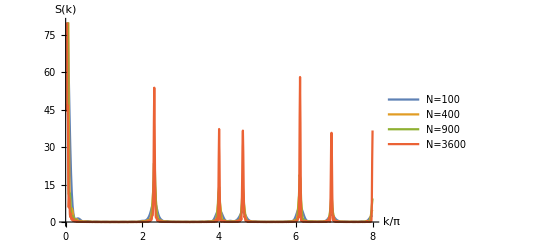

```mathematica
ListLinePlot[{triang100,triang400,triang900,triang3600},PlotRange->{0,80},PlotLegends->{"N=100","N=400","N=900","N=3600"},AxesLabel->{HoldForm[k/π],HoldForm["S(k)"]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
N[12/(Sqrt[3])]
```

6.9282

```mathematica
triangcsv = Import["C:\\Users\\Nora\\Documents\\G1.5\\StrucFac\\triangleLattice2D900.csv",{"Data"}]
```

{{0.,0.,900.},{0.,0.05,172.131},{0.,0.1,35.4309},{0.,0.15,0.630547},25914,{8.,7.9,0.910988},{8.,7.95,0.592818},{8.,8.,0.0580487}}
 |  |  |  |

```mathematica
ListPlot3D[triangcsv,PlotRange->{0,100}]
```

-Graphics3D-

```mathematica
ListDensityPlot[triangcsv,Mesh->All,MeshFunctions->Automatic]
```

-Graphics-

## 2D ideal gas

```mathematica
ideal2D = data[[All,7;;10]];
```

```mathematica
ideal100 = ideal2D[[All,{1,2}]];
```

```mathematica
ideal400 = ideal2D[[All,{1,3}]];
```

```mathematica
ideal900 = ideal2D[[All,{1,4}]];
```

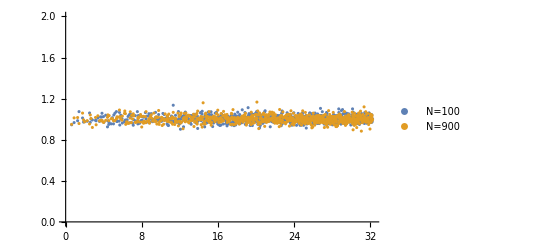

```mathematica
ListPlot[{ideal100,ideal900},PlotRange->{0,2},PlotLegends->{"N=100","N=900"}]
```

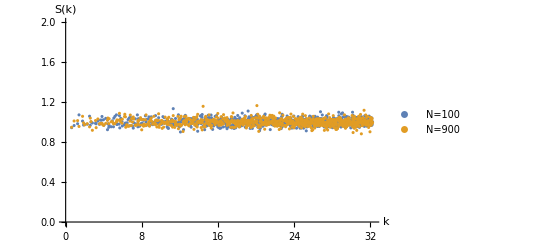

```mathematica
Show[%102,AxesLabel->{HoldForm[k],HoldForm["S(k)"]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

## 1D lattice

```mathematica
data1D=Import["C:\\Users\\Nora\\Documents\\G1.5\\StrucFac\\plot.xlsx",{"Data",1}];
```

```mathematica
lat1D = data1D[[All,1;;5]];
```

```mathematica
lat1D5 = lat1D[[All,{1,2}]];
lat1D10 = lat1D[[All,{1,3}]];
```

```mathematica
lat1D20 = lat1D[[All,{1,4}]];
```

```mathematica
lat1D40 = lat1D[[All,{1,5}]];
```

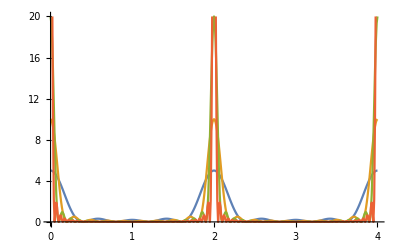

```mathematica
ListLinePlot[{lat1D5,lat1D10,lat1D20,lat1D40},PlotRange->{0,20}]
```

```mathematica
S[k_,n_]:=Norm[Sum[Exp[-I*k*(j/n)],{j,0,n-1}]]^2/n
```

```mathematica
S[k_,n_]:=Sum[Exp[-I*k*(j/n)],{j,0,n-1}]*Sum[Exp[I*k*(j/n)],{j,0,n-1}]/n
```

```mathematica
Simplify[ExpToTrig[S[k,2]]]
```

1+Cos[k/2]

```mathematica
Simplify[ExpToTrig[S[k,3]]]
```

1/3 (1+2 Cos[k/3])^2

```mathematica
Simplify[ExpToTrig[S[k,4]]]
```

(Cos[k/8]+Cos[(3 k)/8])^2

```mathematica
Simplify[ExpToTrig[S[k,5]]]
```

1/5 (1+2 Cos[k/5]+2 Cos[(2 k)/5])^2

```mathematica
Simplify[ExpToTrig[S[k,6]]]
```

2/3 (Cos[k/12]+Cos[k/4]+Cos[(5 k)/12])^2

```mathematica
Simplify[ExpToTrig[S[k,7]]]
```

1/7 (1+2 Cos[k/7]+2 Cos[(2 k)/7]+2 Cos[(3 k)/7])^2

```mathematica
Simplify[ExpToTrig[S[k,8]]]
```

1/2 (Cos[k/16]+Cos[(3 k)/16]+Cos[(5 k)/16]+Cos[(7 k)/16])^2

```mathematica
Simplify[ExpToTrig[S[k,9]]]
```

1/9 (1+2 Cos[k/9]+2 Cos[(2 k)/9]+2 Cos[k/3]+2 Cos[(4 k)/9])^2

```mathematica
Simplify[ExpToTrig[S[k,10]]]
```

2/5 (Cos[k/20]+Cos[(3 k)/20]+Cos[k/4]+Cos[(7 k)/20]+Cos[(9 k)/20])^2

```mathematica
Simplify[ExpToTrig[S[k,N]]]
```

(Csc[k/(2 N)]^2 Sin[k/2]^2)/N

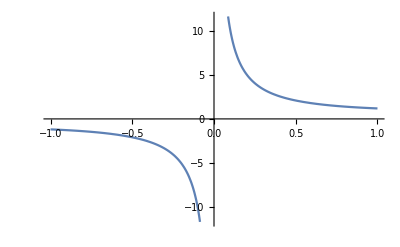

```mathematica
Plot[Csc[x],{x,-1,1}]
```

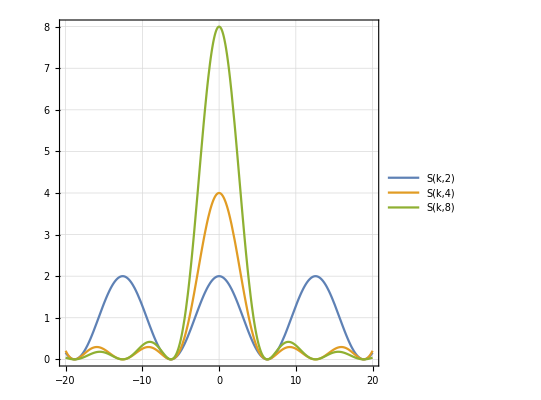

```mathematica
Plot[{S[k,2],S[k,4],S[k,8]},{k,-20,20},PlotRange->{0,8},AspectRatio->1,PlotTheme->"Detailed"]
```

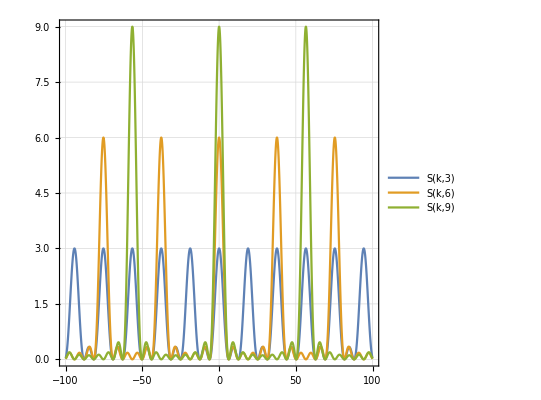

```mathematica
Plot[{S[k,3],S[k,6],S[k,9]},{k,-100,100},PlotRange->{0,9},AspectRatio->1,PlotTheme->"Detailed"]
```

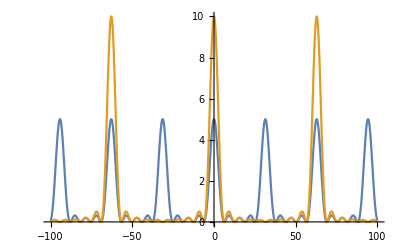

```mathematica
Plot[{S[k,5],S[k,10]},{k,-100,100},PlotRange->{0,10}]
```

## 1D ideal gas

```mathematica
gas1D = data1D[[All,6;;10]];
```

```mathematica
gas1D5 = gas1D[[All,{1,2}]];
gas1D10 = gas1D[[All,{1,3}]];
```

```mathematica
gas1D40 = gas1D[[All,{1,4}]];
```

```mathematica
gas1D160 = gas1D[[All,{1,5}]];
```

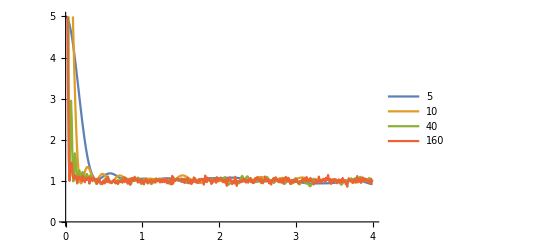

```mathematica
ListLinePlot[{gas1D5,gas1D10,gas1D40,gas1D160},PlotRange->{0,5},PlotLegends->{"5","10","40","160"}]
```

## Moving to 3D: uniformly sample the surface of a unit sphere

```mathematica
sphereUniform = Import["C:\\Users\\Nora\\Documents\\G1.5\\StrucFac\\sphereUniform.csv",{"Data"}];
```

```mathematica
ListPointPlot3D[sphereUniform,PlotStyle->Blue,BoxRatios->{1,1,1}]
```

-Graphics3D-

## 3D equilibrium hard sphere

Assuming D = 1.

```mathematica
a1[ϕ_]:=(1+2 ϕ)^2/(1-ϕ)^4
```

```mathematica
a2[ϕ_]:=-(1+ϕ/2)^2/(1-ϕ)^4
```

```mathematica
c[q_,ϕ_]:=-4*Pi/q^3(a1[ϕ]*(Sin[q]-q*Cos[q])+6*ϕ*a2[ϕ]/q*(2*q*Sin[q]+(2-q^2)*Cos[q]-2)+ϕ*a1[ϕ]/(2*q^3)*(4*q*(q^2-6)*Sin[q]-(24-12*q^2+q^4)*Cos[q]+24))
```

```mathematica
ρ[ϕ_]:=6*ϕ/Pi
```

```mathematica
hTilda[k_,ϕ_]:=c[k,ϕ]/(1-ρ[ϕ]*c[k,ϕ])
```

```mathematica
hTilda[2,0.2]
```

-1.88951

```mathematica
S3d[k_,ϕ_]:=hTilda[k,ϕ]*ρ[ϕ]+1
```

```mathematica
S3d[2*Pi,0.2]
```

1.23654

```mathematica
S3d[4*Pi,0.2]
```

1.05389

```mathematica
h2[r_,ϕ_]:=1/(2*Pi^2*r)*NIntegrate[hTilda[k,ϕ]*k*Sin[k*r],{k,0,Infinity}]
```

```mathematica
result=Table[{i*0.1+0.001,h2[i*0.1+0.001,0.2]},{i,0,40}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {169.667}. NIntegrate obtained -0.0201823 and 0.0000484743 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {169.667}. NIntegrate obtained -1.99367 and 0.000201806 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {169.667}. NIntegrate obtained -3.96751 and 0.000121362 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{0.001,-1.02245},{0.101,-1.00001},{0.201,-0.999982},{0.301,-0.999999},{0.401,-1.00001},{0.501,-1.},{0.601,-0.999999},{0.701,-0.999997},{0.801,-1.},{0.901,-0.999981},{1.001,0.716646},{1.101,0.520706},{1.201,0.355012},{1.301,0.219402},{1.401,0.112746},{1.501,0.033299},{1.601,-0.0209535},{1.701,-0.0520846},{1.801,-0.0621336},{1.901,-0.052899},{2.001,-0.0260615},{2.101,0.000128101},{2.201,0.0124862},{2.301,0.0156209},{2.401,0.0133183},{2.501,0.00851989},{2.601,0.00334895},{2.701,-0.000816708},{2.801,-0.00327157},{2.901,-0.00389992},{3.001,-0.00309715},{3.101,-0.00165891},{3.201,-0.000320079},{3.301,0.000572993},{3.401,0.000955811},{3.501,0.000925823},{3.601,0.000648716},{3.701,0.000292099},{3.801,-0.0000158154},{3.901,-0.000204993},{4.001,-0.000263597}}

```mathematica
h2theory=result;
```

```mathematica
h2data=Import["C:\\Users\\Nora\\Documents\\G1.5\\StrucFac\\plot.xlsx",{"Data",4}];
```

```mathematica
h2simu = h2data[[All,{4,6}]];
```

```mathematica
Dimensions[h2simu]
```

{500,2}

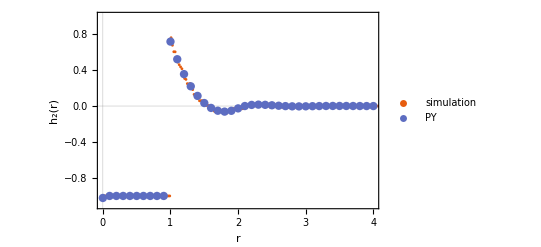

```mathematica
h2Plot=ListPlot[{h2simu,h2theory},PlotLegends->{"simulation","PY"},PlotTheme->"Scientific",PlotRange->{{0,4},{-1.1,1}},PlotStyle->{PointSize[0.005],PointSize[0.015]},FrameLabel->{{HoldForm["h_2(r)"],None},{HoldForm[r],None}}]
```

```mathematica
hTildaBrute[k_]:=(2*Pi)^(3/2)*Sum[(h2simu[[i,1]])^2*h2simu[[i,2]]*BesselJ[0.5,k*h2simu[[i,1]]]/((k*h2simu[[i,1]])^0.5)*0.02,{i,1,500}]
```

```mathematica
hTildaBrute[2]
```

-1.89352

```mathematica
Sbrute[k_]:=hTildaBrute[k]*ρ[0.2]+1
```

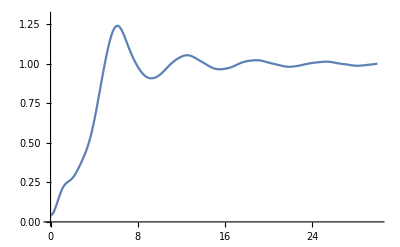

```mathematica
Plot[Sbrute[x],{x,0,30},PlotRange->{0,1.3}]
```

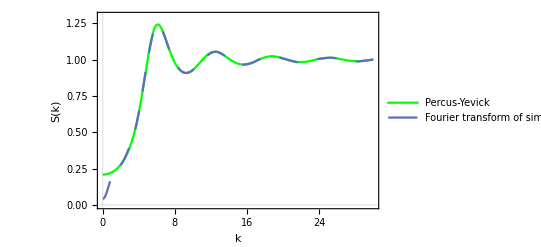

```mathematica
theory=Plot[{S3d[x,0.2],Sbrute[x]},{x,0,30},PlotRange->{0,1.3},PlotTheme->Scientific,FrameLabel->{{HoldForm["S(k)"],None},{HoldForm[k],None}},PlotLabel->None,LabelStyle->{GrayLevel[0]},PlotStyle->{Green,Dashing[Large]},PlotLegends->{"Percus-Yevick","Fourier transform of simulated h_2(r)"}]
```

```mathematica
data3D=Import["C:\\Users\\Nora\\Documents\\G1.5\\StrucFac\\plot.xlsx",{"Data",3}];
```

```mathematica
skHardSphere = data3D[[All,{6,7}]];
```

```mathematica
simu=ListPlot[skHardSphere,PlotRange->{0,1.3},PlotStyle->{Directive[Red,PointSize[0.005]]},PlotLegends->{"Direct from definition"}];
```

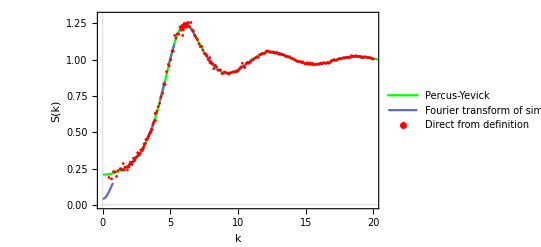

```mathematica
Show[theory,simu,PlotRange->{{0,20},{0,1.3}}]
```